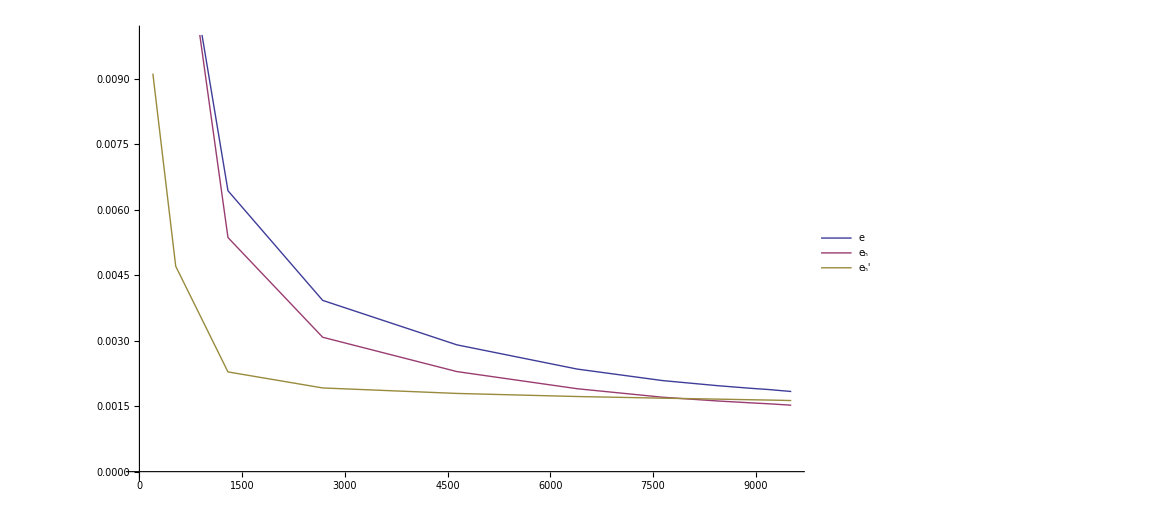

```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem2\\my\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];


ListLinePlot[{
	Transpose[{triangles, realErr}],
	Transpose[{triangles, myErr}],
	Transpose[{triangles, ostErr}]
},
PlotLegends->Placed[{
ToExpression["e",TeXForm,HoldForm],
ToExpression["e_h",TeXForm,HoldForm],
ToExpression["e_h^\prime",TeXForm,HoldForm]
},{0.8,.5}],
BaseStyle->{FontWeight->"Bold",FontSize->18},
PlotRange -> {0,0.010}
]
```

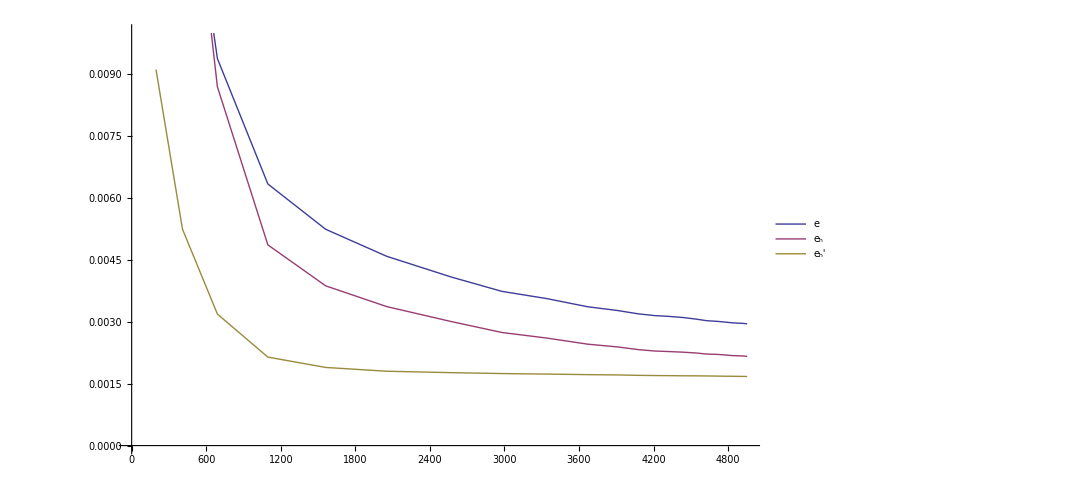

```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem2\\ost\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];

ListLinePlot[{
	Transpose[{triangles, realErr}],
	Transpose[{triangles, myErr}],
	Transpose[{triangles, ostErr}]
},

PlotLegends->Placed[{
ToExpression["e",TeXForm,HoldForm],
ToExpression["e_h",TeXForm,HoldForm],
ToExpression["e_h^\prime",TeXForm,HoldForm]
},{0.8,.5}],
BaseStyle->{FontWeight->"Bold",FontSize->18},
PlotRange -> {0,0.010}
]
```